```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/428fstep3.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

80

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata=Take[rawdata,All,2];
```

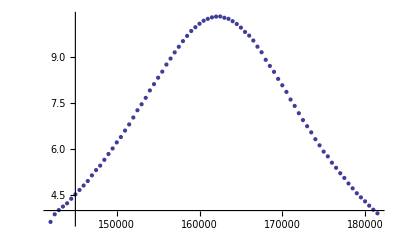

```mathematica
dataplot=ListPlot[plotdata]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[i]]],{max}=freq[[i]]}],{i,1,num}]
```

42{162500.,10.329}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[plotdata,model,{x0,g,b},x,MaxIterations->1000]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.2594×10^-17, -4.68452×10^-13, -4.68452×10^-13}, {0., « 1 », -« 23 »}, {0., 0., -« 24 »}} may contain significant numerical errors.

{BestFitParameters→{x0→6.34585×10^6,g→83.1259,b→83.1259},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 6.34585×10^6 | 2.93702×10^22 | {-5.84836×10^22,5.84836×10^22}
g | 83.1259 | 2.62849×10^25 | {-5.23399×10^25,5.23399×10^25}
b | 83.1259 | 2.62849×10^25 | {-5.23399×10^25,5.23399×10^25},EstimatedVariance→58.1727,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 6.59629×10^-8 | 2.19876×10^-8
Error | 77 | 4479.3 | 58.1727
Uncorrected Total | 80 | 4479.3 | 
Corrected Total | 79 | 369.298 | ,AsymptoticCorrelationMatrix→(1. | -1. | 1.
-1. | 1. | -1.
1. | -1. | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 1.14672×10^22
Max Parameter-Effects | 2.33688×10^37
95. % Confidence Region | 0.605967}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

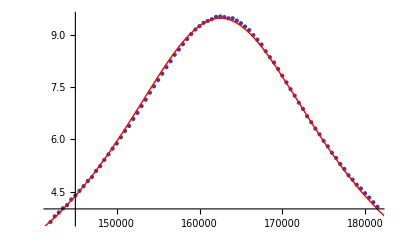

```mathematica
Show[dataplot,fitplot]
```